# Piece of Cake coordinates

## Coordinate system description

The coordinates used here are based upon https://arxiv.org/abs/gr-qc/0512001v1.
Each patch will use local coordinates labeled (a,b,c) limited to the [-1,1] range and is embedded in a global Cartesian coordinate system with coordinates (x,y,z).  The c coordinate is radial while the remaining two are angular. The +x patch is defined and all other patches are rotations of it.

## Patch system skeleton

```mathematica
ClearAll[CakePlusX];
CakePlusX={
baseX[a,b,c],
baseY[a,b,c],
baseZ[a,b,c]
};

ClearAll[CakeMinusX];
CakeMinusX=RotationMatrix[π,{0,0,1}].CakePlusX;

ClearAll[CakePlusY];
CakePlusY=RotationMatrix[π/2,{0,0,1}].CakePlusX;

ClearAll[CakeMinusY];
CakeMinusY=RotationMatrix[-π/2,{0,0,1}].CakePlusX;

ClearAll[CakePlusZ];
CakePlusZ=RotationMatrix[-π/2,{0,1,0}].CakePlusX;

ClearAll[CakeMinusZ];
CakeMinusZ=RotationMatrix[π/2,{0,1,0}].CakePlusX;

ClearAll[InverseCakePlusX];
InverseCakePlusX={
baseA[x,y,z],
baseB[x,y,z],
baseC[x,y,z]
};

ClearAll[InverseCakeMinusX];
InverseCakeMinusX=RotationMatrix[π,{0,0,1}].InverseCakePlusX;

ClearAll[InverseCakePlusY];
InverseCakePlusY=RotationMatrix[π/2,{0,0,1}].InverseCakePlusX;

ClearAll[InverseCakeMinusY];
InverseCakeMinusY=RotationMatrix[-π/2,{0,0,1}].InverseCakePlusX;

ClearAll[InverseCakePlusZ];
InverseCakePlusZ=RotationMatrix[-π/2,{0,1,0}].InverseCakePlusX;

ClearAll[InverseCakeMinusZ];
InverseCakeMinusZ=RotationMatrix[π/2,{0,1,0}].InverseCakePlusX;
```

## Base Coordinate transformations

```mathematica
ClearAll[baseX,baseY,baseZ];
baseX[a_,b_,c_]=(r0(1-c)+r1(1+c))/(√(4+2 a^2 (1+c)+2 b^2 (1+c)));
baseY[a_,b_,c_]=b*baseX[a,b,c];
baseZ[a_,b_,c_]=a*baseX[a,b,c];

ClearAll[baseA,baseA,baseA];
baseC[x_,y_,z_]=(r0^2-r1^2+y^2+z^2+√(4 r1^2 x^2+(y^2+z^2)^2+4 r0^2 (x^2+y^2+z^2)-4 r0 r1 (2 x^2+y^2+z^2)))/(r0-r1)^2;
baseB[x_,y_,z_]=y/x;
baseA[x_,y_,c_]=z/x;
```

## Visualising patches

### 3D Patch Plotting routine

```mathematica
ClearAll[AssertAbort];
AssertAbort[cond_,msg_]:=If[cond==False,Print[msg];Abort[];];

ClearAll[PlotPatch3D]
PlotPatch3D[color_,patchName_,R0_,Rf_,surface_]:=Block[
{
r0=R0,
r1=Rf,
c=surface
},
AssertAbort[-1≤surface≤1,"The surface parameter must be inside the (-1,1) interval"];

Return[
ParametricPlot3D[
Evaluate[patchName],

{b,-1,1},
{a,-1,1},

PlotPoints->30,
MaxRecursion->2,

PlotRange->Full,

BoundaryStyle->Directive[Black,Thick],

PlotStyle->color,

MeshStyle->Directive[Black,Thin],

MeshFunctions->{Function[{x,y,z,b,c},c],Function[{x,y,z,b,c},b]},

AxesLabel->{"x","y","z"}
]
];
];
```

### 3D Plots

```mathematica
Manipulate[
Block[{c,R0,Rf},
c=cval;

R0=1;
Rf=10;

Show[
PlotPatch3D[Red,CakePlusX,R0,Rf,c],
PlotPatch3D[Green,CakeMinusX,R0,Rf,c],
PlotPatch3D[Blue,CakePlusY,R0,Rf,c],
PlotPatch3D[Orange,CakeMinusY,R0,Rf,c],
PlotPatch3D[Yellow,CakePlusZ,R0,Rf,c],
PlotPatch3D[White,CakeMinusZ,R0,Rf,c],

PlotRange->{{-Rf,Rf},{-Rf,Rf},{-Rf,Rf}},

AxesLabel->{"x","y","z"},
ViewPoint->{∞,∞,∞},
Axes->False,
Boxed->False,
ImageSize->Large,

PlotLabel->"c="<>ToString[c]
]
],
{cval,-1,1}
]
```

### 2D Slices

```mathematica
CakePlusX
```

{((1-c) r0+(1+c) r1)/(√(4+2 a^2 (1+c)+2 b^2 (1+c))),(b ((1-c) r0+(1+c) r1))/(√(4+2 a^2 (1+c)+2 b^2 (1+c))),(a ((1-c) r0+(1+c) r1))/(√(4+2 a^2 (1+c)+2 b^2 (1+c)))}

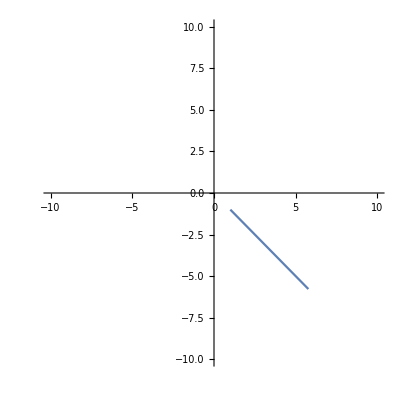

```mathematica
Block[{r0,r1,a,b},
r0=1;
r1=10;
a=-1;
b=-1;
ParametricPlot[{CakePlusX⟦1⟧,CakePlusX⟦2⟧},{c,-1,1},PlotRange->{{-r1,r1},{-r1,r1}}]
]
```

## Jacobians and code generation

Recall the our global to local transformations are

baseX(a,b,c)=core(a,b,c)
baseY(a,b,c)=b*baseX(a,b,c)
baseZ(a,b,c)=c*baseX(a,b,c),

where

core(a,b,c)=(f-a f+Rf+a Rf)/(√2 √(2+(1+a) b^2+(1+a) c^2))

Thus all derivatives can be computed in terms of the core function.

### Jacobians

Since all patches are rotations of the +X patch, we compute derivatives only once

```mathematica
ClearAll[baseX,baseY,baseZ];
baseX[a_,b_,c_]:=core[a,b,c];
baseY[a_,b_,c_]:=b*baseX[a,b,c];
baseZ[a_,b_,c_]:=c*baseX[a,b,c];

ClearAll[coords,functions,functionsName];
coords={a,b,c};
functions=CakePlusZ;
functionsName="CAKE_PLUS_Z";

ClearAll[derivativeRules];
derivativeRules={
ToString[D[core[a,b,c],a],CForm]->"d_core_da",
ToString[D[core[a,b,c],b],CForm]->"d_core_db",
ToString[D[core[a,b,c],c],CForm]->"d_core_dc",

ToString[D[core[a,b,c],{a,2}],CForm]->"d2_core_da_da",
ToString[D[core[a,b,c],{b,2}],CForm]->"d2_core_db_db",
ToString[D[core[a,b,c],{c,2}],CForm]->"d2_core_dc_dc",

ToString[D[core[a,b,c],a,b],CForm]->"d2_core_da_db",
ToString[D[core[a,b,c],a,c],CForm]->"d2_core_da_dc",
ToString[D[core[a,b,c],b,c],CForm]->"d2_core_db_dc",

ToString[core[a,b,c],CForm]->"core"
};

ClearAll[J];
(* da/dx[i,j]=da[i]/dx[j] *)
J[i_,j_]:=FullSimplify[D[functions⟦i⟧,coords⟦j⟧]];

ClearAll[dJ];
(* d^2a/dx^2[i,j,k]=d^2a[i]/dx^2[j,k] *)
dJ[i_,j_,k_]:=FullSimplify[D[functions⟦i⟧,coords⟦j⟧,coords⟦k⟧]];

(* Transform to code *)
WriteString["stdout","#define "<>functionsName<>"_JACOBIAN "]
ClearAll[i,j,k];
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
WriteString["stdout","J("<>ToString[i-1]<>")("<>ToString[j-1]<>") = "<>StringReplace[ToString[J[i,j],CForm],derivativeRules]<>";"];
]
]
WriteString["stdout","\n\n"]

WriteString["stdout","#define "<>functionsName<>"_DJACOBIAN "]
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
WriteString["stdout","dJ("<>ToString[i-1]<>")("<>ToString[j-1]<>","<>ToString[k-1]<>") = "<>StringReplace[ToString[dJ[i,j,k],CForm],derivativeRules]<>";"];
]
]
]
ClearAll[i,j,k];
```

#define CAKE_PLUS_Z_JACOBIAN J(0)(0) = -(c*d_core_da);J(0)(1) = -(c*d_core_db);J(0)(2) = -core - c*d_core_dc;J(1)(0) = b*d_core_da;J(1)(1) = core + b*d_core_db;J(1)(2) = b*d_core_dc;J(2)(0) = d_core_da;J(2)(1) = d_core_db;J(2)(2) = d_core_dc;

#define CAKE_PLUS_Z_DJACOBIAN dJ(0)(0,0) = -(c*d2_core_da_da);dJ(0)(0,1) = -(c*d2_core_da_db);dJ(0)(0,2) = -d_core_da - c*d2_core_da_dc;dJ(0)(1,0) = -(c*d2_core_da_db);dJ(0)(1,1) = -(c*d2_core_db_db);dJ(0)(1,2) = -d_core_db - c*d2_core_db_dc;dJ(0)(2,0) = -d_core_da - c*d2_core_da_dc;dJ(0)(2,1) = -d_core_db - c*d2_core_db_dc;dJ(0)(2,2) = -2*d_core_dc - c*d2_core_dc_dc;dJ(1)(0,0) = b*d2_core_da_da;dJ(1)(0,1) = d_core_da + b*d2_core_da_db;dJ(1)(0,2) = b*d2_core_da_dc;dJ(1)(1,0) = d_core_da + b*d2_core_da_db;dJ(1)(1,1) = 2*d_core_db + b*d2_core_db_db;dJ(1)(1,2) = d_core_dc + b*d2_core_db_dc;dJ(1)(2,0) = b*d2_core_da_dc;dJ(1)(2,1) = d_core_dc + b*d2_core_db_dc;dJ(1)(2,2) = b*d2_core_dc_dc;dJ(2)(0,0) = d2_core_da_da;dJ(2)(0,1) = d2_core_da_db;dJ(2)(0,2) = d2_core_da_dc;dJ(2)(1,0) = d2_core_da_db;dJ(2)(1,1) = d2_core_db_db;dJ(2)(1,2) = d2_core_db_dc;dJ(2)(2,0) = d2_core_da_dc;dJ(2)(2,1) = d2_core_db_dc;dJ(2)(2,2) = d2_core_dc_dc;

## Scratch space